```mathematica
hori=Import["/Users/blmayer/doctorate/thesis/primes/horizontal.csv"];
```

```mathematica
hori=hori[[2;;]];
```

```mathematica
horigo=#[[1]]->#[[2]]&/@hori//Flatten;
```

```mathematica
igv2=Graph[horigo, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv2];
```

```mathematica
degree=VertexDegree[igv2]//Mean//N;
```

```mathematica
count = Total[adj]//Counts
```

<|1→2,2→179,3→111,5→42,4→93,6→38,8→13,9→5,7→12,10→2,11→2,12→1|>

```mathematica
countrel = Table[{x,Lookup[count,x]/500}, {x,Keys[count]}][[2;;]]
```

{{2,179/500},{3,111/500},{5,21/250},{4,93/500},{6,19/250},{8,13/500},{9,1/100},{7,3/125},{10,1/250},{11,1/250},{12,1/500}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.12203/x^1.57276]

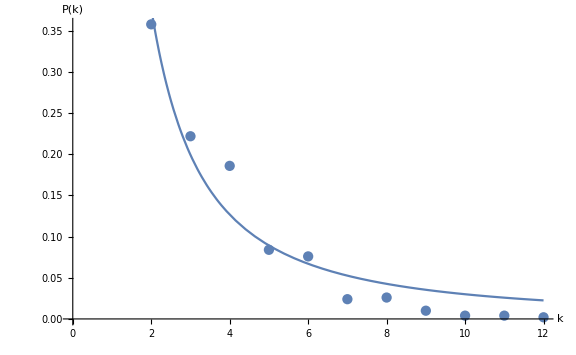

```mathematica
vis2=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]
```

{horizontal,11,500,3.58,1.57276 ± 0.377857,1.12203 ± 0.423911}

## natural

```mathematica
visibles={{{1->2,1->3,1->4,1->5,1->6,1->7,1->8,1->9,1->11,1->12,1->14,1->15,1->16,1->18,1->19,1->21,1->22,1->23,1->24,1->27,1->29,1->30,1->32,1->34,1->36,1->37,11411,488->489,489->490,489->491,489->496,489->497,489->499,490->491,491->492,491->493,491->494,491->496,491->497,491->499,492->493,492->494,493->494,494->495,494->496,494->497,495->496,495->497,496->497,497->498,497->499,498->499,499->500}}, {{{, , , , }}}};
```

```mathematica
nat=Import["/Users/blmayer/doctorate/thesis/primes/natural.csv"];
```

```mathematica
nat=nat[[2;;]];
```

```mathematica
gonat=#[[1]]->#[[2]]&/@nat//Flatten;
```

```mathematica
gonat
```

{1→2,1→4,1→6,1→8,1→9,1→11,1→15,1→16,1→18,2→3,2→4,2→9,2→11,2→15,2→16,2→18,3→4,3→9,3→11,3→15,3→16,4→5,4→6,4→8,4→9,4→11,4→15,4→16,5→6,6→7,6→8,6→9,7→8,7→9,8→9,9→10,9→11,9→15,9→16,10→11,11→12,11→14,11→15,11→16,12→13,12→14,12→15,13→14,13→15,14→15,15→16,16→17,16→18,17→18,18→19,19→20}

```mathematica
igv2=Graph[gonat, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv2];
```

```mathematica
count = Total[adj]//Counts
```

<|1→2,2→172,3→103,4→87,5→49,6→36,9→8,7→12,8→14,11→5,10→7,12→3,14→1,15→1|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}][[2;;]]
```

{{2,43/125},{3,103/500},{4,87/500},{5,49/500},{6,9/125},{9,2/125},{7,3/125},{8,7/250},{11,1/100},{10,7/500},{12,3/500},{14,1/500},{15,1/500}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.05328/x^1.54823]

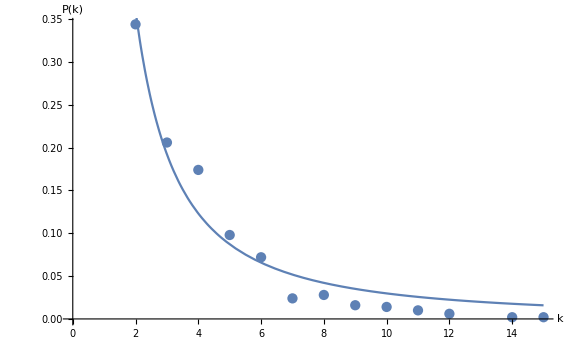

```mathematica
vis2=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```